```mathematica
EdgeList[CycleGraph[5]]
```

{1<->2,1<->5,2<->3,3<->4,4<->5}

```mathematica
Map[#[[1]]+5<->#[[2]]+5&,{1<->2,1<->5,2<->3,3<->4,4<->5}]
```

{6<->7,6<->10,7<->8,8<->9,9<->10}

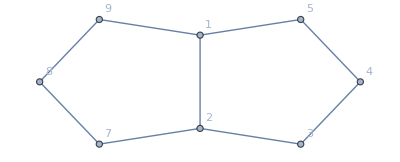

```mathematica
g=Graph[VertexContract[VertexContract[ Graph[{1<->2,1<->5,2<->3,3<->4,4<->5,6<->7,6<->10,7<->8,8<->9,9<->10}],{1,10}],{2,6}],VertexLabels->"Name"]
```

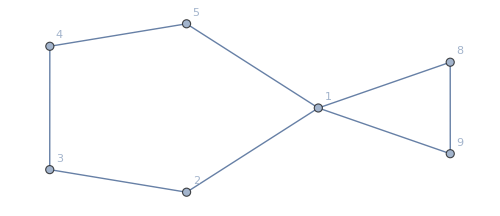
{-Graphics-, | 1 | 2 | 3 | 4 | 5 | 8 | 9
1 | 60
0 | 0
60 | 18
42 | 18
42 | 0
60 | 0
60 | 0
60
2 |  | 60
0 | 0
60 | 18
42 | 18
42 | 20
40 | 20
40
3 |  |  | 60
0 | 0
60 | 18
42 | 14
46 | 14
46
4 |  |  |  | 60
0 | 0
60 | 14
46 | 14
46
5 |  |  |  |  | 60
0 | 20
40 | 20
40
8 |  |  |  |  |  | 60
0 | 0
60
9 |  |  |  |  |  |  | 60
0}

```mathematica
ColorMainMatrix[VertexContract[g,{1,7}],Graph[#,VertexLabels->"Name",ImageSize->500]&]
```

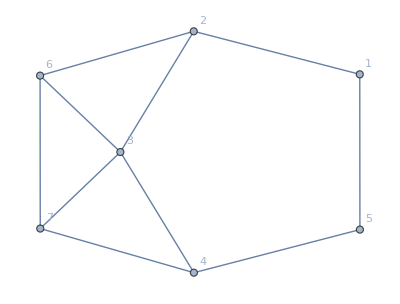

```mathematica
g=Graph[{1<->2,1<->5,2<->3,3<->4,4<->5,6<->7,6<->2,7<->4,7<->3,6<->3},VertexLabels->"Name"]
```

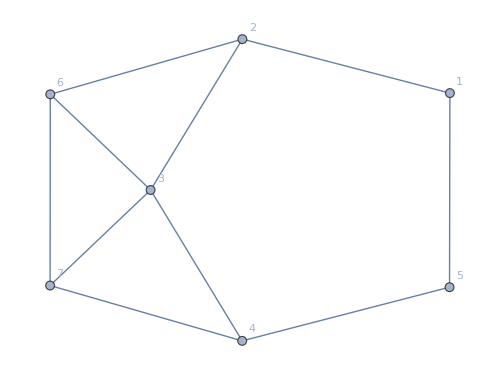
{-Graphics-, | 1 | 2 | 3 | 4 | 5 | 6 | 7
1 | 27
0 | 0
27 | 8
19 | 9
18 | 0
27 | 10
17 | 4
23
2 |  | 27
0 | 0
27 | 6
21 | 9
18 | 0
27 | 14
13
3 |  |  | 27
0 | 0
27 | 8
19 | 0
27 | 0
27
4 |  |  |  | 27
0 | 0
27 | 14
13 | 0
27
5 |  |  |  |  | 27
0 | 4
23 | 10
17
6 |  |  |  |  |  | 27
0 | 0
27
7 |  |  |  |  |  |  | 27
0}

```mathematica
ColorMainMatrix[g,Graph[#,VertexLabels->"Name",ImageSize->500]&]
```

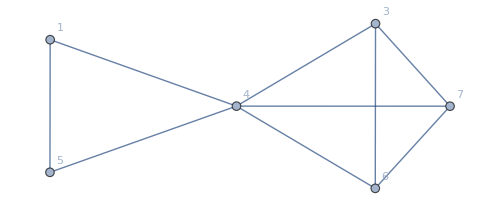
{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7
1 | 6
0 | 2
4 | 0
6 | 0
6 | 2
4 | 2
4
3 |  | 6
0 | 0
6 | 2
4 | 0
6 | 0
6
4 |  |  | 6
0 | 0
6 | 0
6 | 0
6
5 |  |  |  | 6
0 | 2
4 | 2
4
6 |  |  |  |  | 6
0 | 0
6
7 |  |  |  |  |  | 6
0}

```mathematica
ColorMainMatrix[VertexContract[g,{4,2}],Graph[#,VertexLabels->"Name",ImageSize->500]&]
```

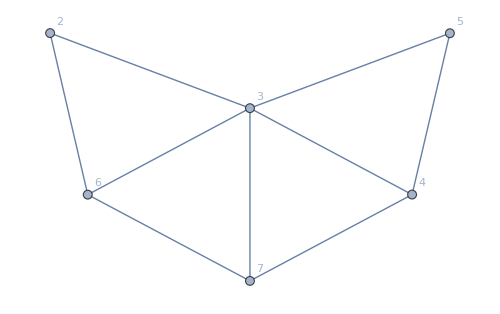
{-Graphics-, | 2 | 3 | 4 | 5 | 6 | 7
2 | 8
0 | 0
8 | 2
6 | 3
5 | 0
8 | 4
4
3 |  | 8
0 | 0
8 | 0
8 | 0
8 | 0
8
4 |  |  | 8
0 | 0
8 | 4
4 | 0
8
5 |  |  |  | 8
0 | 2
6 | 4
4
6 |  |  |  |  | 8
0 | 0
8
7 |  |  |  |  |  | 8
0}

```mathematica
ColorMainMatrix[VertexContract[g,{3,1}],Graph[#,VertexLabels->"Name",ImageSize->500]&]
```

```mathematica
ChromaticPolynomial[EdgeContract[VertexDelete[Graph[plantri[[100]]],2],1<->7],x]
```

-153680718 x+826872913 x^2-2069257193 x^3+3219753714 x^4-3506815206 x^5+2848903733 x^6-1793450184 x^7+895895329 x^8-360202996 x^9+117379338 x^10-31025711 x^11+6616102 x^12-1124254 x^13+148991 x^14-14863 x^15+1051 x^16-47 x^17+x^18

```mathematica
-153680718 x+826872913 x^2-2069257193 x^3+3219753714 x^4-3506815206 x^5+2848903733 x^6-1793450184 x^7+895895329 x^8-360202996 x^9+117379338 x^10-31025711 x^11+6616102 x^12-1124254 x^13+148991 x^14-14863 x^15+1051 x^16-47 x^17+x^18/.x->4
```

1944

```mathematica
Factor[30 x-95 x^2+128 x^3-96 x^4+42 x^5-10 x^6+x^7]
```

(-2+x) (-1+x) x (15-25 x+19 x^2-7 x^3+x^4)

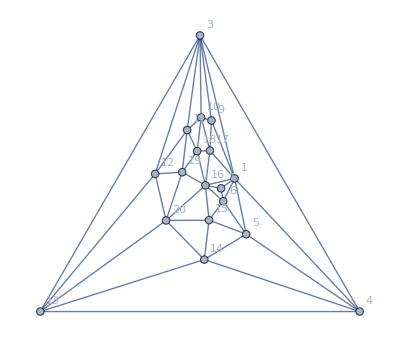

```mathematica
Graph[VertexContract[VertexDelete[Graph[plantri[[100]]],2],{1,8}],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

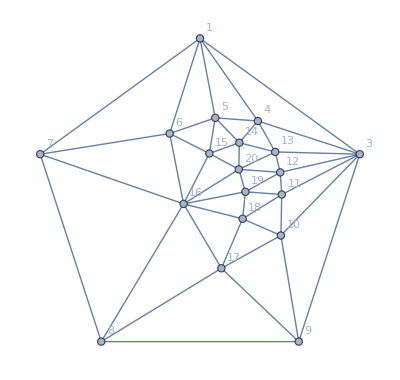

```mathematica
Graph[VertexContract[VertexDelete[Graph[plantri[[100]]],2],1<->8],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

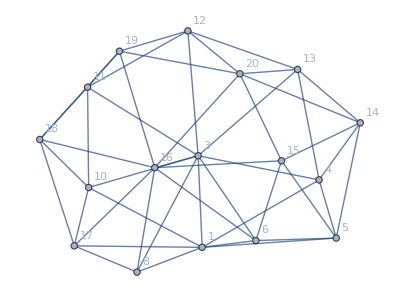

```mathematica
Graph[VertexContract[VertexContract[VertexDelete[Graph[plantri[[100]]],2],{3,7}],{1,9}],VertexLabels->"Name"]
```